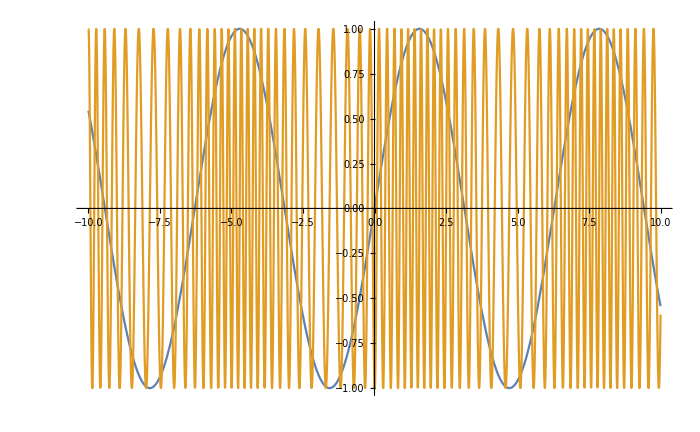

```mathematica
f1[x_]:=Sin[x];
c1[x_]:=Sin[10*x];
Plot[{f1[x],Sin[20*x+(-Cos[x]*8)]},{x,-10,10},ImageSize->700]
(*p:=Range[-10,10,.01]
ListLinePlot[{f1[p],c1[(f1[p]+1)/2*p]},ImageSize->800]*)
```

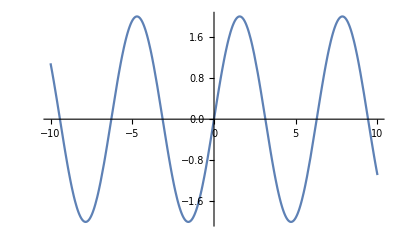

```mathematica
f1[x_]:=2Sin[x]
f2[x_]:=Cos[2x]
s1[x_]:=Sin[x]
Plot[{f1[x]},{x,-10,10}]
```

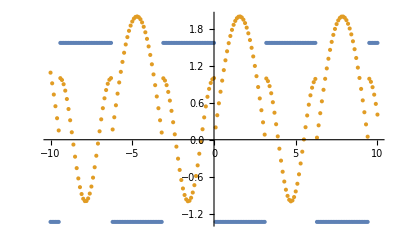

```mathematica
ff[x_]:=If[s1[x]>0,f1[x],f2[x]]
d[x_]:=ff[x]*f2[x]
nrst:=Function[x,Sort[Nearest[Range[-5Pi,5Pi,Pi],x,2],#1<#2&]];
rng:=Range[-10,10,0.1];

dd:=Function[x,
n:=nrst[x];
NIntegrate[d[q],{q,n[[1]],n[[2]]}]
];

ListPlot[{Map[dd,rng],Map[ff,rng]},DataRange->{-10,10}]
```